# Clear console

```mathematica
Quiet@Remove["Global`*"]
SetDirectory[NotebookDirectory[]];
```

# Parameters

```mathematica
nmax=175;
var={u,v};
par={s,r};
nvar=Length[var];
fixedpar={};
parval={r->0,s->0}//N;
ηval={ηNF->0}//N;
ξval={ξNF->0}//N;
κval={κNF^2->ⅈ/2}//N;
C11eval={C11->0.740082804492285*ⅈ}//N;
A3eval={Subscript[ANF, 3]->-0.462551752807678}//N;
```

# Equation

```mathematica
kinetics={r*u-u-2*v+s*u^3-u^5,v};
diffmatrix=({{0, -1}, {-1, 0}});
eq=Solve[kinetics==0,var][[1]];
jacmat=D[kinetics,{var}]/.eq;
kinetics=kinetics/.Table[var[[varnum]]->var[[varnum]]+(var[[varnum]]/.eq),{varnum,nvar}];
```

# Kernel of the Jacobian matrix

```mathematica
dummymat=Table[Subscript[dmat, row,col],{row,nvar},{col,nvar}];
dummyvec=Table[Subscript[dvec, varnum],{varnum,nvar}];
jacobianmat=jacmat-μNF*diffmatrix/.fixedpar;
Tcond2=D[Det[jacobianmat],μNF];
μval=Solve[Tcond2==0,μNF][[1]]/.parval;
ϕNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
getout=0;
For[row=1,row<=nvar,row++,
If[getout==1,
Break[]];
For[col=1,col<=nvar,col++,
submatrixrows=Complement[Range[nvar],{row}];
submatrixcols=Complement[Range[nvar],{col}];
If[Det[jacobianmat[[submatrixrows,submatrixcols]]/.μval/.parval]!=0,
criticalrow=row;
criticalcol=col;
getout=1;
Break[];
]
];
]
ϕNF[[criticalcol]]=1;
ϕsol=Solve[Dot[jacobianmat[[submatrixrows,submatrixcols]],ϕNF[[submatrixcols]]]==-jacobianmat[[submatrixrows,{criticalcol}]],ϕNF[[submatrixcols]]][[1]];
ϕNF=ϕNF/.ϕsol;
Subscript[sol, 1,1]=Table[Subscript[WNF, 1,1,varnum]->C11*ϕNF[[varnum]],{varnum,nvar}];
```

# Kernel of the adjoint

```mathematica
ψNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
ψNF[[criticalrow]]=1;
ψsol=Solve[Dot[Transpose[jacobianmat[[submatrixrows,submatrixcols]]],ψNF[[submatrixrows]]]==-Transpose[jacobianmat[[{criticalrow},submatrixcols]]],ψNF[[submatrixrows]]][[1]];
ψNF=ψNF/.ψsol/.fixedpar;
```

# Variables to expand

```mathematica
jacobianmat=jacobianmat/.parval;
jacobianmatr=jacmat-rNF^2*μNF*diffmatrix/.parval/.fixedpar;
ϕNF=ϕNF/.μval/.parval/.C11eval;
ψNF=ψNF/.μval/.parval;
Subscript[sol, 1,1]=Subscript[sol, 1,1]/.μval/.parval/.C11eval;
negativetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,-nmax,-1}];
positivetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,1,nmax}];
solr1=LinearSolve[dummymat[[submatrixrows,submatrixcols]],dummyvec[[submatrixcols]]];
solrn1=LinearSolve[dummymat,dummyvec];
toexpand=Flatten[Table[Subscript[var⟦varnum⟧, order]->Sum[Subscript[WNF, order,sub,varnum] ⅇ^(ⅈ sub x)/.Subscript[WNF, order,sub,varnum]->If[sub<0,(-1)^order*ⅇ^(2*sub*ξNF*π)*Conjugate[Subscript[WNF, order,-sub,varnum]]/.ξval,Subscript[WNF, order,sub,varnum]],{sub,-order,order,2}],{order,nmax},{varnum,nvar}]];
toexpand=toexpand/. Subscript[sol, 1,1];
expr=kinetics/.Table[var[[varnum]]->∑_(order=1)^nmax ϵNF^order*Subscript[var[[varnum]], order],{varnum,nvar}]/.parval/.fixedpar;
derivative=D[expr,ϵNF];
```

# Iterative solver

```mathematica
load=1;
SetDirectory[NotebookDirectory[]];
If[FileExistsQ["savedSession.mx"] && load==1,
<<savedSession.mx
,
solvcond={};
ampeval={};
AppendTo[solvcond,0];
]
For[order=If[solvcond=={},2,Length[solvcond]+1],order<=nmax,order++,
save=0;
Print["order="<>ToString[order]];
derivative=D[derivative,ϵNF];
toexpand=toexpand/.ampeval;
equation=1/(order!)*derivative/.ϵNF->0/.toexpand;
equation=Expand[equation]/.negativetab;
If[OddQ[order],
sub=1;
auxeq=1/(2π)∫_0^(2π) equation*ⅇ^(-ⅈ*sub*x)ⅆx;
auxeq=-auxeq/.Flatten[Table[Subscript[WNF, order,aux,varnum]->0,{aux,-order,order,2},{varnum,nvar}]]//Simplify;
If[order>=3,
If[order-2>=sub && OddQ[order],
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=sub && OddQ[order],
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
AppendTo[solvcond,Chop[Dot[auxeq,ψNF]/.μval/.fixedpar]//Simplify];
If[order>=7 && OddQ[order],
solvcond[[order]]=solvcond[[order]]/.Subscript[ANF, order-2]->0;
If[order==7,
partialsol=A3eval;
,
actualeq=solvcond[[order]];
partialsol=Quiet@NSolve[actualeq==0,Subscript[ANF, order-4],Complexes][[1]];
];
ampeval=Join[ampeval,partialsol];
];
auxeq=auxeq/.ampeval;
usefulvec=Table[Subscript[auxvec, order,sub,varnum],{varnum,nvar}];
auxsol=solr1/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}];
usefulvec[[submatrixcols]]=Table[Subscript[WNF, order,sub,submatrixcols[[varnum]]]->auxsol[[varnum]]+Subscript[ANF, order]*ϕNF[[submatrixcols[[varnum]]]],{varnum,nvar-1}];
usefulvec[[criticalcol]]=Subscript[WNF, order,sub,criticalcol]->Subscript[ANF, order]*ϕNF[[criticalcol]];
Subscript[sol, order,sub]=usefulvec/.μval/.C11eval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
,
AppendTo[solvcond,0];
];
For[sub=If[EvenQ[order],0,3],sub<=order,sub+=2,
save=1;
If[sub==0,
auxeq=equation/.positivetab;
,
auxeq=equation/.ⅇ^(ⅈ*sub*x)->1/.positivetab;
];
auxeq=-auxeq/.Flatten[Table[Subscript[WNF, order,aux,varnum]->0,{aux,-order,order,2},{varnum,nvar}]]//Simplify;
If[order>=3,
If[order-2>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
auxsol=solrn1/.Flatten[Table[dummymat[[row,col]]->jacobianmatr[[row,col]]/.rNF->sub,{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}]/.μval/.C11eval;
Subscript[sol, order,sub]=Table[Subscript[WNF, order,sub,varnum]->auxsol[[varnum]],{varnum,nvar}]/.ampeval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
If[sub==0,
equation=equation-(Expand[equation]/.positivetab);
]
];
If[save==1 && sub==order+2,
DumpSave["savedSession.mx",{"Global`","Subscript"}]
]
]
```

order=2

order=3

order=4

order=5

order=6

order=7

order=8

order=9

order=10

order=11

order=12

order=13

order=14

order=15

order=16

order=17

order=18

order=19

order=20

order=21

order=22

order=23

order=24

order=25

order=26

order=27

order=28

order=29

order=30

order=31

order=32

order=33

order=34

order=35

order=36

order=37

order=38

order=39

order=40

order=41

order=42

order=43

order=44

order=45

order=46

order=47

order=48

order=49

order=50

order=51

order=52

order=53

order=54

order=55

order=56

order=57

order=58

order=59

order=60

order=61

order=62

order=63

order=64

order=65

order=66

order=67

order=68

order=69

order=70

order=71

order=72

order=73

order=74

order=75

order=76

order=77

order=78

order=79

order=80

order=81

order=82

order=83

order=84

order=85

order=86

order=87

order=88

order=89

order=90

order=91

order=92

order=93

order=94

order=95

order=96

order=97

order=98

order=99

order=100

order=101

order=102

order=103

order=104

order=105

order=106

order=107

order=108

order=109

order=110

order=111

order=112

order=113

order=114

order=115

order=116

order=117

order=118

order=119

order=120

order=121

order=122

order=123

order=124

order=125

order=126

order=127

order=128

order=129

order=130

order=131

order=132

order=133

order=134

order=135

order=136

order=137

order=138

order=139

order=140

order=141

order=142

order=143

order=144

order=145

order=146

order=147

order=148

order=149

order=150

order=151

order=152

order=153

order=154

order=155

order=156

order=157

order=158

order=159

order=160

order=161

order=162

order=163

order=164

order=165

order=166

order=167

order=168

order=169

order=170

order=171

order=172

order=173

order=174

order=175

# Tabulating information

```mathematica
SetDirectory[NotebookDirectory[]];
<<savedSession.mx
PrependTo[ampeval,Subscript[ANF, 1]->C11/.C11eval];
c10tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,1,varnum],{varnum,nvar}]/. Subscript[sol, order,1],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.κval/.ηval/.C11eval,{order,1,Length[solvcond]-4,2}];
c30tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,3,varnum],{varnum,nvar}]/. Subscript[sol, order,3],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.κval/.ηval/.C11eval,{order,3,Length[solvcond]-4,2}];
c10tab=Table[{Abs[c10tabaux[[ind]]],Arg[c10tabaux[[ind]]]},{ind,Length[c10tabaux]}];
c10tab[[All,1]]
c30tab=Table[{Abs[c30tabaux[[ind]]],Arg[c30tabaux[[ind]]]},{ind,Length[c30tabaux]}];
c30tab[[All,1]]
```

{0.370041,0.0308368,0.0791445,0.0415295,0.0670539,0.0559153,0.0719929,0.0680091,0.0786845,0.0769187,0.0842118,0.0831508,0.0882757,0.0874568,0.0911696,0.0904584,0.093232,0.0925917,0.0947235,0.0941434,0.0958241,0.0952988,0.0966534,0.0961782,0.0972908,0.0968609,0.0977896,0.0974003,0.0981864,0.0978331,0.0985065,0.098185,0.0987681,0.0984747,0.0989842,0.0987157,0.0991646,0.0989182,0.0993164,0.0990896,0.0994453,0.099236,0.0995556,0.0993619,0.0996504,0.0994707,0.0997326,0.0995654,0.0998041,0.0996482,0.0998666,0.099721,0.0999216,0.0997853,0.0999701,0.0998422,0.100013,0.0998929,0.100051,0.0999382,0.100085,0.0999788,0.100116,0.100015,0.100143,0.100048,0.100168,0.100078,0.10019,0.100105,0.100211,0.100129,0.100229,0.100151,0.100245,0.100172,0.100261,0.10019,0.100274,0.100207,0.100287,0.100223,0.100298,0.100237,0.100309,0.10025}

{0.,0.0144547,0.0238503,0.0355183,0.0443702,0.0532571,0.0599455,0.0662089,0.0708714,0.0751643,0.0783479,0.0813002,0.0834894,0.0855572,0.0870914,0.0885746,0.0896748,0.0907657,0.0915734,0.0923955,0.0930023,0.0936359,0.0941015,0.0946,0.0949641,0.0953635,0.0956532,0.0959784,0.0962126,0.0964812,0.096673,0.0968978,0.0970567,0.0972469,0.0973801,0.0975427,0.0976554,0.0977956,0.0978918,0.0980136,0.0980964,0.098203,0.0982748,0.0983688,0.0984313,0.0985147,0.0985695,0.0986439,0.0986922,0.0987588,0.0988017,0.0988617,0.0988999,0.0989541,0.0989882,0.0990374,0.0990681,0.0991129,0.0991405,0.0991815,0.0992065,0.0992441,0.0992667,0.0993013,0.0993219,0.0993538,0.0993726,0.0994021,0.0994193,0.0994466,0.0994624,0.0994878,0.0995023,0.099526,0.0995393,0.0995614,0.0995738,0.0995944,0.0996058,0.0996252,0.0996358,0.0996539,0.0996638,0.0996808,0.09969}

# Plotting

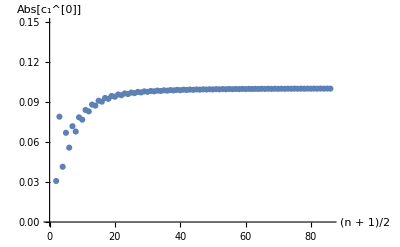

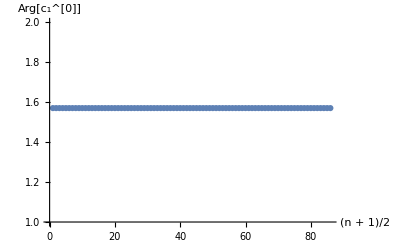

```mathematica
c10tabplotabs=ListPlot[Table[{n,c10tab[[n,1]]},{n,Length[c10tab]}],PlotRange->{{0,Length[c10tab]},{0.0,0.15}},AxesLabel->{"(n + 1)/2","Abs[c_1^[0]]"},BaseStyle->Directive[FontSize->15]]
c10tabplotangle=ListPlot[Table[{n,c10tab[[n,2]]},{n,Length[c10tab]}],PlotRange->{{0,Length[c10tab]},{1.0,2}},AxesLabel->{"(n + 1)/2","Arg[c_1^[0]]"},BaseStyle->Directive[FontSize->15]]
```

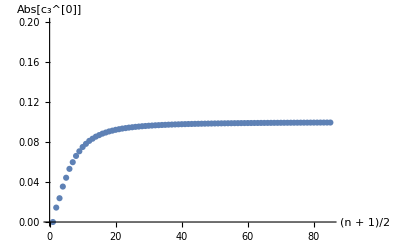

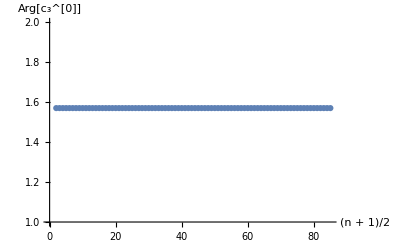

```mathematica
c30tabplotabs=ListPlot[Table[{n,c30tab[[n,1]]},{n,Length[c30tab]}],PlotRange->{{0,Length[c30tab]},{0.0,0.2}},AxesLabel->{"(n + 1)/2","Abs[c_3^[0]]"},BaseStyle->Directive[FontSize->15]]
c30tabplotangle=ListPlot[Table[{n,c30tab[[n,2]]},{n,Length[c30tab]}],PlotRange->{{0,Length[c30tab]},{1.0,2}},AxesLabel->{"(n + 1)/2","Arg[c_3^[0]]"},BaseStyle->Directive[FontSize->15]]
```

{param_0→0.10142,param_1→-0.0564395,param_2→-1.589}

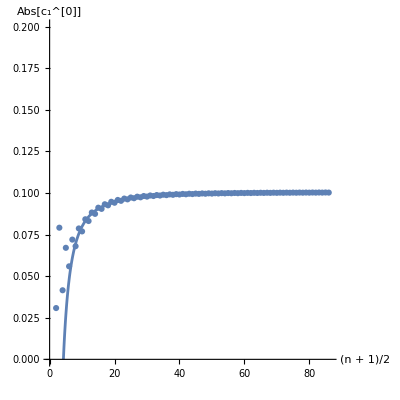

```mathematica
c10funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c10tab[[n,1]]},{n,9,Length[c10tab]}],c10funabs,parameters,n]
fitplot=Plot[c10funabs/.fitpar,{n,0,Length[c10tab]},PlotRange->{{0,Length[c10tab]+0.5},{0.0,0.2}},AxesLabel->{"(n + 1)/2","Abs[c_1^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c10tabplotabs]
```

{param_0→1.5708,param_1→1.28702×10^-14,param_2→2.02306×10^-15}

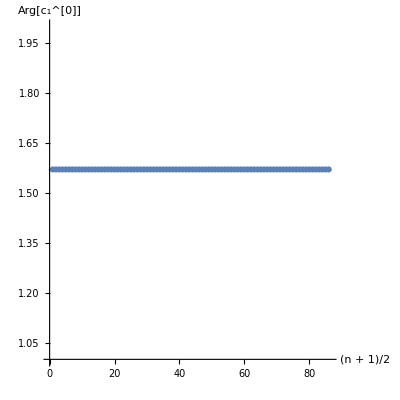

```mathematica
c10funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c10tab[[n,2]]},{n,9,Length[c10tab]}],c10funangle,parameters,n]
fitplot=Plot[c10funangle/.fitpar,{n,0,Length[c10tab]},PlotRange->{{0,Length[c10tab]+0.5},{1.0,2}},AxesLabel->{"(n + 1)/2","Arg[c_1^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c10tabplotangle]
```

{param_0→0.101189,param_1→-0.0910112,param_2→-1.70856}

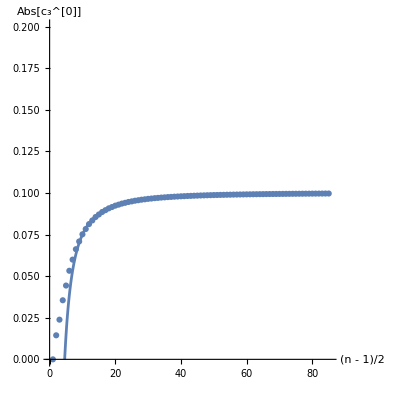

```mathematica
c30funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c30tab[[n,1]]},{n,9,Length[c30tab]}],c30funabs,parameters,n]
fitplot=Plot[c30funabs/.fitpar,{n,0,Length[c30tab]},PlotRange->{{0,Length[c30tab]+0.5},{0.0,0.2}},AxesLabel->{"(n - 1)/2","Abs[c_3^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c30tabplotabs]
```

{param_0→1.5708,param_1→5.25129×10^-14,param_2→-5.79008×10^-13}

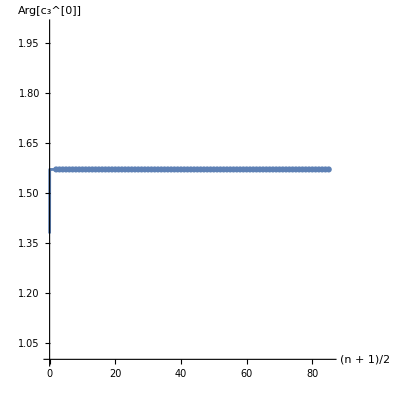

```mathematica
c30funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c30tab[[n,2]]},{n,9,Length[c30tab]}],c30funangle,parameters,n]
fitplot=Plot[c30funangle/.fitpar,{n,0,Length[c30tab]},PlotRange->{{0,Length[c30tab]+0.5},{1.0,2}},AxesLabel->{"(n + 1)/2","Arg[c_3^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c30tabplotangle]
```